```mathematica
Clear["Global`*"]
```

### Set initial values:

```mathematica
coord={time,r,θ,ϕ};
M=1;
gamma0 =1;
gamma1=-1;
gamma2=1;
Psi00=-1.0+2*M/r;
Psi01=2*M/r;
Psi02=0;
Psi03=0;
Psi11=1+2*M/r;
Psi12=0;
Psi13=0;
Psi22=r^2;
Psi23=0;
Psi33=r^2 Sin[θ]^2;
psi={{Psi00, Psi01, Psi02, Psi03},{Psi01,Psi11,Psi12,Psi13},{Psi02,Psi12,Psi22,Psi23},{Psi03,Psi13,Psi23,Psi33}};
```

### Compute other values:

```mathematica
invPsi=Inverse[psi];
affine=Table[(1/2)*Sum[(invPsi[[i,s]])*
(D[psi[[s,j]],coord[[k]] ]+
D[psi[[s,k]],coord[[j]] ]-D[psi[[j,k]],coord[[s]] ]),{s,1,4}],
{i,1,4},{j,1,4},{k,1,4}] ;
phi=Simplify[Table[D[psi[[a,b]],coord[[i]]],{i,1,4},{a,1,4},{b,1,4}]];
g=Table[psi[[i,j]],{i,2,4},{j,2,4}];
invG=Inverse[g];
lapse=(Sum[psi[[1,i+1]]*psi[[1,j+1]]*invG[[i,j]],{i,1,3},{j,1,3}]-psi[[1,1]])^0.5;
shift=Table[Sum[psi[[1,j+1]]*invG[[j,i]],{j,1,3}],{i,1,3}];
tensorGamma=Table[0.5*(phi[[b,a,c]]+phi[[c,a,b]]-phi[[a,b,c]]),{a,1,4},{b,1,4},{c,1,4}];
vecGamma=Table[Sum[invPsi[[b,c]]*tensorGamma[[a,b,c]],{b,1,4},{c,1,4}],{a,1,4}];
H=Table[-vecGamma[[a]],{a,1,4}];
deriH=Table[D[H[[b]],coord[[a]]],{a,1,4},{b,1,4}];
gradH=Table[deriH[[a,b]]-Sum[affine[[c,a,b]]*H[[c]],{c,1,4}],{a,1,4},{b,1,4}];
t={1/lapse,-shift[[1]]/lapse,-shift[[2]]/lapse,-shift[[3]]/lapse};
pi=Table[-Sum[t[[c]]*phi[[c,a,b]],{c,1,4}],{a,1,4},{b,1,4}];
```

### Put real variables back:

```mathematica
psi[[2,2]]=g11[time,r];
pi[[2,2]]=pi11[time,r];
phi[[2,2,2]]=phi11[time,r];

g=Table[psi[[i,j]],{i,2,4},{j,2,4}];
invPsi=Inverse[psi];
invG=Inverse[g];
lapse=(Sum[psi[[1,i+1]]*psi[[1,j+1]]*invG[[i,j]],{i,1,3},{j,1,3}]-psi[[1,1]])^0.5;
shift=Table[Sum[psi[[1,j+1]]*invG[[j,i]],{j,1,3}],{i,1,3}];
phi[[1]]=Table[-lapse*pi[[a,b]]+Sum[shift[[i]]*phi[[i+1,a,b]],{i,1,3}],{a,1,4},{b,1,4}];
tensorGamma=Table[0.5*(phi[[b,a,c]]+phi[[c,a,b]]-phi[[a,b,c]]),{a,1,4},{b,1,4},{c,1,4}];
vecGamma=Table[Sum[invPsi[[b,c]]*tensorGamma[[a,b,c]],{b,1,4},{c,1,4}],{a,1,4}];
t={1/lapse,-shift[[1]]/lapse,-shift[[2]]/lapse,-shift[[3]]/lapse};
```

### Compute source terms:

```mathematica
rhsPsi=Table[-lapse*pi[[a,b]]-gamma1*Sum[shift[[i]]*phi[[i+1,a,b]],{i,1,3}],{a,1,4},{b,1,4}];
t1rhsPhi=Table[0.5*lapse*Sum[t[[c]]*t[[d]]*phi[[i+1,c,d]],{c,1,4},{d,1,4}]*pi[[a,b]],{i,1,3},{a,1,4},{b,1,4}];
t2rhsPhi=Table[lapse*Sum[invG[[j,k]]*t[[c]]*phi[[i+1,j+1,c]]*phi[[k+1,a,b]],{j,1,3},{k,1,3},{c,1,4}],{i,1,3},{a,1,4},{b,1,4}];
t3rhsPhi=Table[-lapse*gamma2*phi[[i+1,a,b]],{i,1,3},{a,1,4},{b,1,4}];
t1rhsPi=Table[2*lapse*Sum[invPsi[[c,d]]*(Sum[invG[[i,j]]*phi[[i+1,c,a]]*phi[[j+1,d,b]],{i,1,3},{j,1,3}]-pi[[c,a]]*pi[[d,b]]-Sum[invPsi[[e,f]]*tensorGamma[[a,c,e]]*tensorGamma[[b,d,f]],{e,1,4},{f,1,4}]),{c,1,4},{d,1,4}],{a,1,4},{b,1,4}];
t2rhsPi=Table[-lapse*(gradH[[a,b]]+gradH[[b,a]]),{a,1,4},{b,1,4}];
t3rhsPi=Table[-0.5*lapse*Sum[t[[c]]*t[[d]]*pi[[c,d]]*pi[[a,b]],{c,1,4},{d,1,4}],{a,1,4},{b,1,4}];
t4rhsPi=Table[-lapse*Sum[t[[c]]*pi[[c,i+1]]*invG[[i,j]]*phi[[j+1,a,b]],{i,1,3},{j,1,3},{c,1,4}],{a,1,4},{b,1,4}];
t5rhsPi=Table[lapse*gamma0*Sum[(KroneckerDelta[c,a]*Sum[psi[[b,d]]*t[[d]],{d,1,4}]+KroneckerDelta[c,b]*Sum[psi[[a,d]]*t[[d]],{d,1,4}]-psi[[a,b]]*t[[c]])*(H[[c]]+vecGamma[[c]]),{c,1,4}],{a,1,4},{b,1,4}];
t6rhsPi=Table[-gamma1*gamma2*Sum[shift[[i]]*phi[[i+1,a,b]],{i,1,3}],{a,1,4},{b,1,4}];
rhsPhi=t1rhsPhi+t2rhsPhi+t3rhsPhi;
rhsPi=t1rhsPi+t2rhsPi+t3rhsPi+t4rhsPi+t5rhsPi+t6rhsPi;
```

### Compute the Jacobian of source terms vector and its eigen values:

```mathematica
S=Simplify[{rhsPsi[[2,2]],rhsPi[[2,2]],rhsPhi[[1,2,2]]}];
vec={g11[time,r],pi11[time,r],phi11[time,r]};
jacobianS=Simplify[Table[D[S[[i]],vec[[j]]],{i,1,3},{j,1,3}]];
appJS=Table[S[[i]]/vec[[j]],{i,1,3},{j,1,3}];
```

```mathematica
g11[time,r]=1+2/r;
pi11[time,r]=-(4. (r/(2.+r))^0.5)/r^3;
phi11[time,r]=-2/r^2;
ans=Simplify[Eigenvalues[jacobianS]];
```

```mathematica
F[r_]=pi[[2,2]]*Psi01^2/2/lapse/Psi11^2-Psi01*phi[[2,2,2]]/Psi11^2;
ans1[r_]=ans[[1]];
ans2[r_]=ans[[2]];
ans3[r_]=ans[[3]];
```

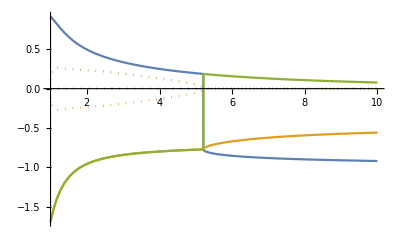

```mathematica
ReImPlot[{ans1[r],ans2[r],ans3[r]},{r,1,10}]
```

{{Null},{Null^2}}

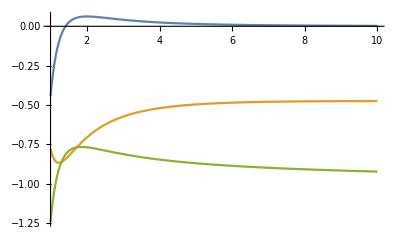

```mathematica
{{js1[r_]=jacobianS[[1,1]];}, {js2[r_]=jacobianS[[2,2]];
js3[r_]=jacobianS[[3,3]];}}
Plot[{js1[r],js2[r],js3[r]},{r,1,10}]
```